```mathematica
dateMouseSessionListV1={{"072920","Mouse21019","Session1"},{"080920","Mouse21019","Session1"},{"081120","Mouse21019","Session2"},{"082620","Mouse21020","Session1"},{"072820","Mouse21036","Session2"},{"080920","Mouse21036","Session2"},{"081120","Mouse21036","Session2"},{"081420","Mouse21036","Session1"},{"080620","Mouse21062","Session2"},{"091920","Mouse21068","Session1"},{"091320","Mouse21068","Session2"},{"111420","Mouse23385","Session1"},{"111620","Mouse23385","Session2"},{"120420","Mouse23385","Session2"},{"121020","Mouse23312","Session1"},{"121320","Mouse23312","Session1"},{"010421","Mouse23332","Session1"},{"010721","Mouse23332","Session1"},{"011221","Mouse23332","Session1"},{"011921","Mouse23332","Session1"},{"011021","Mouse23305","Session1"},{"011221","Mouse23305","Session1"},{"031821","Mouse23324","Session1"},{"030821","Mouse23321","Session2"},{"031821","Mouse23321","Session1"}};
```

```mathematica
dateMouseSessionListV2m={{"090820","Mouse21011","Session3"},{"092120","Mouse21011","Session2"},{"091620","Mouse21069","Session1"},{"100120","Mouse21069","Session1"},{"090420","Mouse21076","Session1"},{"090520","Mouse21076","Session2"},{"111420","Mouse23383","Session1"},{"111620","Mouse23383","Session2"},{"112220","Mouse23383","Session1"},{"111420","Mouse23386","Session1"},{"111720","Mouse23386","Session1"},{"120620","Mouse23383","Session1"},{"010221","Mouse23382","Session1"},{"010421","Mouse23382","Session1"},{"010621","Mouse23382","Session1"},{"011621","Mouse23390","Session1"},{"011721","Mouse23390","Session1"},{"022721","Mouse23310","Session1"},{"031121","Mouse23310","Session2"},{"022021","Mouse23338","Session1"},{"030121","Mouse23338","Session1"},{"031621","Mouse23338","Session2"}};
```

```mathematica
(***************************************************)
```

```mathematica
osiValsV1=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/osiVals_V1.txt","List"]];
```

```mathematica
osiValsV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/osiVals_V2m.txt","List"]];
```

```mathematica
(**********************)
```

```mathematica
v1Charts=Show[BoxWhiskerChart[osiValsV1,{{"Whiskers", Directive[Darker@Blue,Thick]}, {"Fences", Directive[Darker@Blue,Thick]},{"MedianMarker", Directive[Darker@Blue,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Directive[Blue,Opacity[0.3]],Frame->False],DistributionChart[osiValsV1,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Blue],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
pmCharts=Show[BoxWhiskerChart[osiValsV2m,{{"Whiskers", Directive[Darker@Purple,Thick]}, {"Fences", Directive[Darker@Purple,Thick]},{"MedianMarker", Directive[Darker@Purple,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Directive[Purple,Opacity[0.3]],Frame->False],DistributionChart[osiValsV2m,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Purple],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[osiValsV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Transparent,Frame->False],DistributionChart[osiValsV2m,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

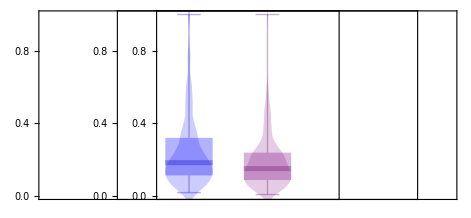

```mathematica
GraphicsRow[{v1Charts,pmCharts,transp},Spacings->{{-280,-280,-320}}]
```

```mathematica
(******)
```

```mathematica
dsiValsV1=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/dsiVals_V1.txt","List"]];
```

```mathematica
dsiValsV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/dsiVals_V2m.txt","List"]];
```

```mathematica
(**********************)
```

```mathematica
v1Charts=Show[BoxWhiskerChart[dsiValsV1,{{"Whiskers", Directive[Darker@Blue,Thick]}, {"Fences", Directive[Darker@Blue,Thick]},{"MedianMarker", Directive[Darker@Blue,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Directive[Blue,Opacity[0.3]],Frame->False],DistributionChart[dsiValsV1,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Blue],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
pmCharts=Show[BoxWhiskerChart[dsiValsV2m,{{"Whiskers", Directive[Darker@Purple,Thick]}, {"Fences", Directive[Darker@Purple,Thick]},{"MedianMarker", Directive[Darker@Purple,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Directive[Purple,Opacity[0.3]],Frame->False],DistributionChart[dsiValsV2m,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Purple],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[dsiValsV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{0,1}},ChartStyle->Transparent,Frame->False],DistributionChart[dsiValsV2m,PlotRange->{All,{0,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

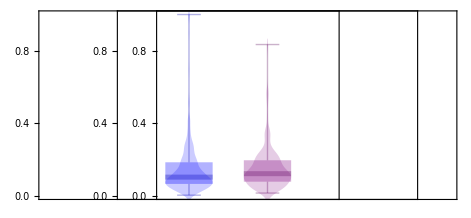

```mathematica
GraphicsRow[{v1Charts,pmCharts,transp},Spacings->{{-280,-280,-320}}];
```